## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 20; mu = 0.3;
```

```mathematica
winit=(0.35-0.00005*I)
```

0.35-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.381104+2.30058×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

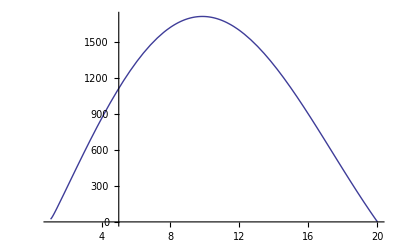

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.35+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.35+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{1.66667,2.30058×10^-8},{1.65,2.09069×10^-8},{1.63333,1.89369×10^-8},{1.61667,1.70899×10^-8},{1.6,1.53629×10^-8},{1.58333,1.37556×10^-8},{1.56667,1.22618×10^-8},{1.55,1.08792×10^-8},{1.53333,9.60405×10^-9},{1.51667,8.43304×10^-9},{1.5,7.36185×10^-9},{1.48333,6.3868×10^-9},{1.46667,5.5034×10^-9},{1.45,4.70683×10^-9},{1.43333,3.99191×10^-9},{1.41667,3.35271×10^-9},{1.4,2.78237×10^-9},{1.38333,2.27266×10^-9},{1.36667,1.81182×10^-9},{1.35,1.39482×10^-9},{1.33333,1.00018×10^-9},{1.31667,6.07358×10^-10},{1.3,2.56661×10^-10},{1.28333,-2.7517×10^-10},{1.26667,-8.41693×10^-10},{1.25,-1.56013×10^-9},{1.23333,-2.49905×10^-9},{1.21667,-3.73692×10^-9},{1.2,-5.39426×10^-9},{1.18333,-7.60039×10^-9},{1.16667,-1.04872×10^-8},{1.15,-1.42456×10^-8},{1.13333,-1.90851×10^-8},{1.11667,-2.52476×10^-8},{1.1,-3.3033×10^-8},{1.08333,-4.26861×10^-8},{1.06667,-5.46279×10^-8},{1.05,-6.92328×10^-8},{1.03333,-8.69409×10^-8},{1.01667,-1.08242×10^-7},{1.,-1.33679×10^-7},{0.983333,-1.63848×10^-7},{0.966667,-1.99405×10^-7},{0.95,-2.41076×10^-7},{0.933333,-2.89646×10^-7},{0.916667,-3.45981×10^-7},{0.9,-4.11025×10^-7},{0.883333,-4.85806×10^-7},{0.866667,-5.71439×10^-7},{0.85,-6.69129×10^-7},{0.833333,-7.80244×10^-7},{0.816667,-9.06145×10^-7},{0.8,-1.04845×10^-6},{0.783333,-1.20877×10^-6},{0.766667,-1.38896×10^-6},{0.75,-1.59098×10^-6},{0.733333,-1.81693×10^-6},{0.716667,-2.06908×10^-6},{0.7,-2.34988×10^-6},{0.683333,-2.66196×10^-6},{0.666667,-3.00816×10^-6},{0.65,-3.3915×10^-6},{0.633333,-3.81525×10^-6},{0.616667,-4.28292×10^-6},{0.6,-4.79822×10^-6},{0.583333,-5.36519×10^-6},{0.566667,-5.9881×10^-6},{0.55,-6.67154×10^-6},{0.533333,-7.42041×10^-6},{0.516667,-8.23992×10^-6},{0.5,-9.13566×10^-6},{0.483333,-0.0000101136},{0.466667,-0.00001118},{0.45,-0.0000123416},{0.433333,-0.0000136057},{0.416667,-0.0000149797},{0.4,-0.0000164719},{0.383333,-0.0000180909},{0.366667,-0.0000198456},{0.35,-0.0000217459},{0.333333,-0.000023802},{0.316667,-0.0000260247},{0.3,-0.0000284255},{0.283333,-0.0000310166},{0.266667,-0.0000338107},{0.25,-0.0000368216},{0.233333,-0.0000400633},{0.216667,-0.0000435512},{0.2,-0.0000473009},{0.183333,-0.0000513294},{0.166667,-0.0000556543},{0.15,-0.0000602939},{0.133333,-0.0000652679},{0.116667,-0.0000705967},{0.1,-0.0000763016},{0.0833333,-0.0000824053},{0.0666667,-0.0000889312},{0.05,-0.000095904},{0.0333333,-0.00010335},{0.0166667,-0.000111295},{0.,-0.000119767}}

```mathematica
(*The imaginary part vs the radius*)
```

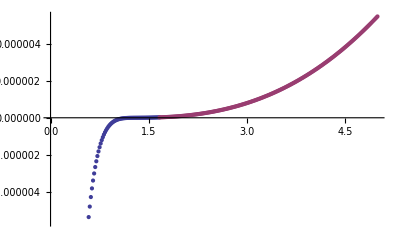

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

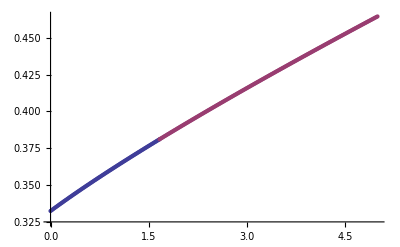

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=20/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=20/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=20/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=20/Q=0.999/I.dat